```mathematica
Quit
```

```mathematica
$HistoryLength=0;
```

## Initialization

### Paths

```mathematica
projectDirectory=ExpandFileName@"~/Documents/unireps";
```

```mathematica
datasetsDirectory=FileNameJoin[{projectDirectory,"datasets"}];
outputsDirectory=FileNameJoin[{projectDirectory,"outputs"}];
```

### Python

```mathematica
py=StartExternalSession[{"Python","Evaluator"-><|
"EnvironmentName"->"unireps",
"PythonRuntime"->"3.11",
"Dependencies"->{
"torch",
"datasets",
"transformers",
"matplotlib",
"numpy"
}
|>}];
```

```mathematica
ExternalEvaluate[py,"
import torch
import datasets
import numpy as np

import sys
sys.path.append(<* ParentDirectory@NotebookDirectory[] *>)
import unireps
"]
```

## Importing embeddings

```mathematica
getDatasetName[{model_,dataset_,chat_:False}]:=
StringReplace[model,"/"->"__"]<>"---"<>dataset<>If[chat,"--chat",""]
```

```mathematica
getDatasetPath[output_]:=
FileNameJoin[{outputsDirectory,getDatasetName[output]}]
```

```mathematica
getDataset[output_]:=
ExternalEvaluate[
py,
<|
"Command"->StringTemplate["datasets.load_from_disk('``')"][getDatasetPath[output]],
"ReturnType"->"ExternalObject"
|>
]
```

```mathematica
getDatasetTexts[output_]:=
ExternalEvaluate[
py,
StringTemplate["datasets.load_from_disk('``')['text']"][getDatasetPath[output]]
]
```

```mathematica
getDatasetTruncation[output_]:=
ExternalEvaluate[
py,
StringTemplate["[b.item() for b in datasets.load_from_disk('``')['at_max_length']]"][getDatasetPath[output]]
]
```

```mathematica
getDatasetEmbeddings[output_,layer_:All,agg_:"Last",normalize_:True]:=
ExternalEvaluate[
py,
StringTemplate[
"np.array(unireps.dataset_embs(datasets.load_from_disk('``'), layer=``, agg='``', normalize=``))"
][
getDatasetPath[output],
Replace[layer,All->"None"],
Replace[agg,{"Last"->"last","Mean"->"mean"}],
normalize
]
]
```

## Similarity measures

### Mutual k-NN

```mathematica
getKNN[embs_,k_]/;ArrayDepth[embs]===2:=Map[e|->Ordering[e,-k],embs.Transpose[embs]-Normal[999999*IdentityMatrix[Length[embs]]]]
getKNN[embs_,k_]/;ArrayDepth[embs]===3:=getKNN[#,k]&/@embs
```

```mathematica
knn1=getKNN[Normal@getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}],10];//EchoTiming
```

17.4523

```mathematica
embs=getDatasetEmbeddings[{"meta-llama/Llama-3.1-70B-Instruct","web_text"},All];//EchoTiming
```

21.9282

```mathematica
embs//Dimensions
```

{81,2048,8192}

```mathematica
embs
```

NumericArray[<81,2048,8192>, Real32]

```mathematica
MemoryInUse[]
```

21966011800

```mathematica
Beep[]
```

```mathematica
knn2=getKNN[Normal@embs,10];//EchoTiming
```

36.6501

```mathematica
knn2=getKNN[Normal@getDatasetEmbeddings[{"meta-llama/Meta-Llama-3.1-8B","web_text"}],10];//EchoTiming
```

0.014883

```mathematica
knn1//Dimensions
```

{43,2048,10}

```mathematica
mutualKNN[knn1_,knn2_]/;ArrayDepth[knn1]===ArrayDepth[knn2]===2:=
With[{k=Dimensions[knn1][[2]]},
Mean[MapThread[N@*Length@*Intersection,{knn1,knn2}]]/k
]
```

```mathematica
ArrayDepth@knn1[[10]]
```

2

```mathematica
mat=Table[mutualKNN[knn1i,knn2i],{knn1i,knn1},{knn2i,knn2}];//EchoTiming
```

7.44451

PlotRange?

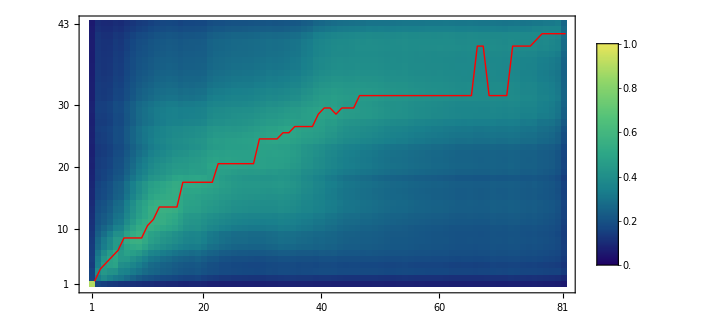

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData["BlueGreenYellow"][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}],Epilog->{Red,Line[MapIndexed[{#2[[1]],Ordering[#1,-1][[1]]}&,Transpose@mat]]},DataReversed->True]
```

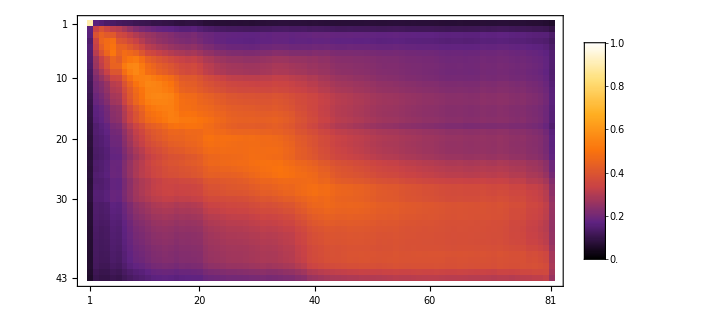

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData["SunsetColors"][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

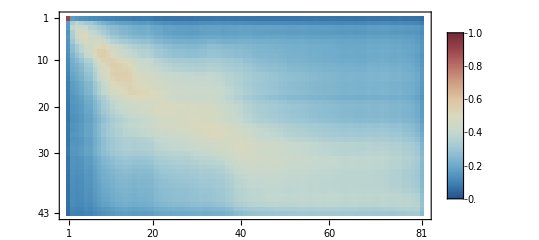

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData[{"RedBlueTones","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

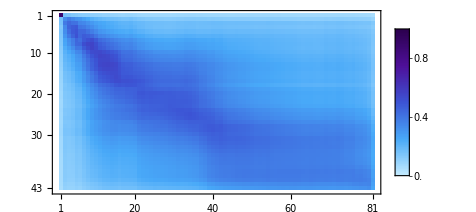

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData[{"DeepSeaColors","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

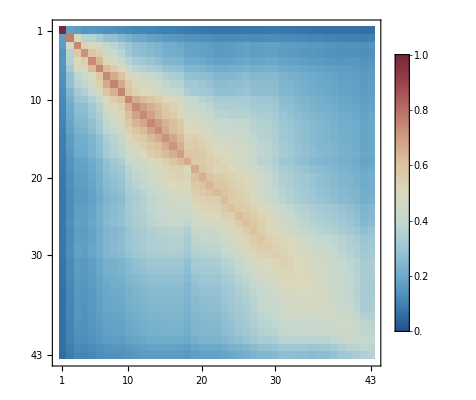

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData[{"RedBlueTones","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

```mathematica
Mean[MapThread[N@*Length@*Intersection,{knn1[[10]],knn2[[20]]}]]/10
```

```mathematica
Mean[MapThread[N@*Length@*Intersection,{knn1[[10]],knn2[[20]]}]]/10
```

0.365186

## Scratch space

```mathematica
Import@getDatasetPath[{"google/gemma-2-9b","web_text"}]
```

{data-00000-of-00006.arrow,data-00001-of-00006.arrow,data-00002-of-00006.arrow,data-00003-of-00006.arrow,data-00004-of-00006.arrow,data-00005-of-00006.arrow,dataset_info.json,state.json}

```mathematica
getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}]//EchoTiming//Dimensions
```

4.61218

{43,2048,3584}

```mathematica
t1=Developer`ToPackedArray@Import[
FileNameJoin[{getDatasetPath[{"google/gemma-2-9b","web_text"}],"data-00000-of-00006.arrow"}],
{"Data",All,2}
];//EchoTiming
```

1.33646

```mathematica
TabularStructure[t1]
```

```mathematica
arrowTest=Import[getDatasetPath[{"google/gemma-2-9b","web_text"}],"ArrowDataset"]
```

Import::general: Error creating dataset. Could not read schema from '/Users/christopher/Documents/unireps/outputs/google__gemma-2-9b---web_text/data-00000-of-00006.arrow'. Is th… file?: Could not open IPC input source '/Users/christopher/Documents/unireps/outputs/google__gemma-2-9b---web_text/data-00000-of-00006.arrow': Not an Arrow file

$Failed

```mathematica
gramMatrix[m_]:=m.Transpose[m]
```

```mathematica
rv[x_,y_]:=Norm[Transpose[x].y,"Frobenius"]^2/(Norm[Transpose[x].x,"Frobenius"]*Norm[Transpose[y].y,"Frobenius"])
```

```mathematica
embs1=getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}];//EchoTiming
```

4.30615

```mathematica
embs2=getDatasetEmbeddings[{"google/gemma-2-9b-it","web_text"}];//EchoTiming
```

8.32576

```mathematica
gramMatrix[Normal@embs1[[1]]]//Dimensions//EchoTiming
```

0.11042

{2048,2048}

```mathematica
rv[gramMatrix@Normal@embs1[[1]],gramMatrix@Normal@embs2[[1]]]
```

0.999859

```mathematica
RepeatedTiming[Normal@embs1[[1]];]
```

{0.00623774,Null}

```mathematica
matRV=Table[rv[gramMatrix@Normal@embs1[[i]],gramMatrix@Normal@embs2[[j]]],{i,Length[embs1]},{j,Length[embs2]}];//EchoTiming
```

838.015

```mathematica
matRV[[7,10]]
```

0.9958

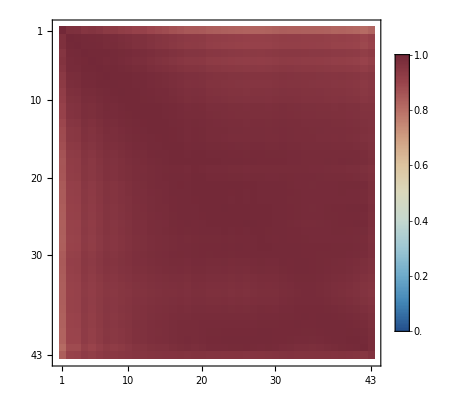

```mathematica
MatrixPlot[matRV,ColorFunction->(ColorData[{"RedBlueTones","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

```mathematica
embs=Normal@getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}];//EchoTiming
```

4.46294

```mathematica
Dimensions@embs
```

{43,2048,3584}

```mathematica
embs[[1]]
```

$Aborted

```mathematica
DistanceMatrix
```

```mathematica
Depth[]
```

```mathematica
ArrayDepth[embs]
```

3

```mathematica
IdentityMatrix[Length[embs[[1]]]]
```

IdentityMatrix[…]

```mathematica
knnMat=getKNN[embs,10];//EchoTiming
```

12.7174

```mathematica
knnMat//Dimensions
```

{43,3584,10}

```mathematica
Dimensions[embs[[1]].Transpose[embs[[1]]]]
```

{2048,2048}

```mathematica
Dimensions@embs
```

{43,2048,3584}

```mathematica
MinMax[embs[[1]].Transpose[embs[[1]]]]
```

{-0.286683,1.}

```mathematica
Dimensions[embs[[1]].Transpose[embs[[1]]]]
```

{2048,2048}

```mathematica
embs[[1]].Transpose[embs[[1]]]-99999*IdentityMatrix[Length[embs[[1]]]]
```

```mathematica
ByteCount@EchoTiming@getDatasetEmbeddings[{"google/gemma-2-9b","book_translations_en"}]
```

4.1349

1262485672

## OLD

```mathematica
Quit
```

```mathematica
Clear[m]
```

```mathematica
m=RandomReal[{0,1},{33,1024,4096}];
```

```mathematica
EchoTiming@Dimensions@Map[layer|->Map[e|->Ordering[e,-10],layer.Transpose[layer]],m]
```

2.21768

{33,1024,10}

```mathematica
Ordering[#,10]&/@(m[[1]].Transpose[m[[1]]])
```

```mathematica
m.Transpose[m]
```

```mathematica
ByteCount@m
```

1107296424